# -Graphics-

## Utilities

```mathematica
myNorm[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]
myNormMass[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2+1]
MS[v_]:=v[[1]]^2-v[[2]]^2-v[[3]]^2-v[[4]]^2
```

```mathematica
Get["/Users/zeno/cLTD-main/cLTD.m"]
Options[cLTD]
SetOptions[cLTD,"FORMpath"->"/usr/local/bin/form"]
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

{loopmom→{k0,k1,k2,k3},FORMpath→form,tFORMpath→tform,WorkingDirectory→/Users/zeno/Documents/,FORM_ID→None,FORMcores→1,OptimizationLVL→0,keep_FORM_script→False,EvalAll→False,NoNumerator→False,FORMsubs→False}

{loopmom→{k0,k1,k2,k3},FORMpath→/usr/local/bin/form,tFORMpath→tform,WorkingDirectory→/Users/zeno/Documents/,FORM_ID→None,FORMcores→1,OptimizationLVL→0,keep_FORM_script→False,EvalAll→False,NoNumerator→False,FORMsubs→False}

## -Graphics-

```mathematica
props1=prop[k,0]*prop[k-l,0]*prop[l,0]*prop[l-m,0]*prop[l+q,0]*prop[k+q,0]
diag1=cLTD[props1,loopmom->{k,l},EvalAll->True];
CForm[diag1[[1]]]
diag1[[2]]
integrand1[ks_,ls_,ms_,ns_]:=diag1[[1]]/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[l,0] prop[l-m,0] prop[k+q,0] prop[l+q,0]

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q)}

-0.015625*(1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E2 + E4 - q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E0 + E1 + E5 - q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E1 + E5 - q(0))) + 1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))) + 1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))) + 1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) + 
      1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))) + 1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 1/((E1 + E4 + E5)*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 1/((E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E2 + E3 - m(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E0 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) + 1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 1/((E1 + E4 + E5)*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E2 + E4 + q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E0 + E1 + E5 + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E0 + E1 + E5 + q(0))) + 1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))) + 1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) + 1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))) + 
      1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) + 1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))) + 1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))) + 1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 1/((E1 + E4 + E5)*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E0 + E4 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E1 + E4 + E5)*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E2 + E3 + m(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E1 + E2)*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 1/((E0 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))))/
    (E0*E1*E2*E3*E4*E5)

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};
N[integrand1[kt,lt,mt,nt],12]
N[(E3+E5-m[0]-q[0])/.diag1[[2]]/.{q[0]->myNorm[mt]+myNormMass[mt-nt]+myNorm[nt],m[0]->-myNorm[mt]}/.{k->kt,l->lt,m->mt,n->nt,q->{0,0,0}}]
N[(myNorm[lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression … encountered.

Indeterminate

0.

0

```mathematica
N[integrand1[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

6.20329278986×10^-9

### CounterTerms

#### Threshold 1

-Graphics-

Two-loop CounterTerm

```mathematica
ct1LTD=-(1/(64 E0 E1 E2 E3 E4 E5))(1/((E1+E4+E5) (E2+E3+m[0]) (E1+E2+E4-q[0]))+1/((E0+E1+E2) (E0+E1+E3+m[0])  (E0+E1+E5-q[0]))+1/((E0+E1+E3+m[0]) (E2+E3+m[0])  (E0+E1+E5-q[0]))+1/((E2+E3+m[0]) (E1+E2+E4-q[0]) (E2+E5-q[0]))+1/((E2+E3+m[0]) (E0+E1+E5-q[0]) (E2+E5-q[0]))+1/((E1+E4+E5) (E2+E3-m[0]) (E1+E3+E4-m[0]-q[0]))+1/((E1+E4+E5) (E1+E2+E4-q[0]) (E1+E3+E4-m[0]-q[0]))+1/( (E1+E2+E4-q[0]) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2) (E2+E3-m[0]) (E3+E5-m[0]-q[0]))+1/((E0+E1+E2)(E0+E1+E5-q[0]) (E3+E5-m[0]-q[0]))+1/((E0+E1+E5-q[0]) (E2+E5-q[0]) (E3+E5-m[0]-q[0]))+1/((E2+E3-m[0])(E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))+1/((E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))+1/((E0+E1+E2) (E2+E3-m[0])(E2+E5+q[0]))+1/((E1+E4+E5) (E2+E3-m[0]) (E2+E5+q[0]))+1/((E0+E1+E2) (E0+E1+E3+m[0]) (E3+E5+m[0]+q[0]))+1/((E1+E4+E5) (E2+E3+m[0]) (E3+E5+m[0]+q[0]))+1/((E0+E1+E3+m[0]) (E2+E3+m[0])(E3+E5+m[0]+q[0]))+1/((E0+E1+E2)(E2+E5+q[0]) (E3+E5+m[0]+q[0]))+1/((E1+E4+E5) (E2+E5+q[0]) (E3+E5+m[0]+q[0])));
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q)}

```mathematica
ct1integrand1[ks_,ls_,ms_,ns_]:=ct1LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
fullCT12L[ks_,ls_,ms_,ns_]:=((1/(2myNorm[ks]Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2] (Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*ct1integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2myNorm[ks])]}
```

```mathematica
N[fullCT12L[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

1.50823563979×10^-9

Series::ztest1: Unable to decide whether numeric quantity 1/2 Log[1+(1+1/2 Power[«2»])^2]-Log[Root[73-88 Power[«2»]+16 Power[«2»]&,4,0]] is equal to zero. Assuming it is.

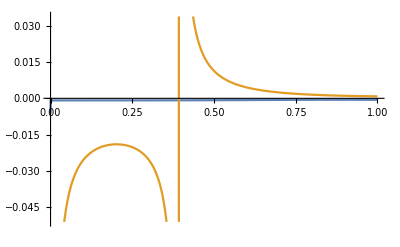

```mathematica
kt={1+Sqrt[3]/2,0,0};
lt={0,1,0};
mt={0,0,1};
nt={0,1,0};

Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}];
Series[fullCT12L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}];

Plot[{integrand1[kt,lt,mt+eps{1,1,0},nt]-fullCT12L[kt,lt,mt+eps{1,1,0},nt],integrand1[kt,lt,mt+eps{1,1,0},nt]},{eps,0,1}]
```

One-loop CounterTerm

```mathematica
fullCT11L[ks_,ls_,ms_,ns_]:=((1/(2Exp[r](Log[myNorm[ks]]-r))*ct1integrand1[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])/2]}
```

```mathematica
N[fullCT11L[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

5.44885556633×10^-9

(2 √(2/(11+4 √3)) (-436-277 √2+20 √3+28 √6-152 √(11+4 √3)-118 √(2 (11+4 √3))+46 √(3 (11+4 √3))+24 √(6 (11+4 √3))))/((2+√2) (√2-√3) (2+√3)^2 (4+√3) (2+√2+√3) (√3-√(11+4 √3)) (2 √2-√3+√(11+4 √3)) (4+√3+√(11+4 √3)) (2 √2+√3+√(11+4 √3)) eps)+O[eps]^0

Series::ztest1: Unable to decide whether numeric quantity Log[2]+Log[1+(√3)/2]-Log[2+√3] is equal to zero. Assuming it is.

-(2 (√(2/(3 (11+4 √3))) (-60-84 √2+436 √3+277 √6-138 √(11+4 √3)-72 √(2 (11+4 √3))+152 √(3 (11+4 √3))+118 √(6 (11+4 √3)))))/(((2+√2) (√2-√3) (2+√3)^2 (4+√3) (2+√2+√3) (√3-√(11+4 √3)) (2 √2-√3+√(11+4 √3)) (4+√3+√(11+4 √3)) (2 √2+√3+√(11+4 √3))) eps)+O[eps]^0

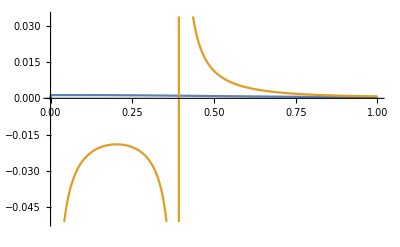

```mathematica
kt={1+Sqrt[3]/2,0,0};
lt={0,1,0};
mt={0,0,1};
nt={0,1,0};

Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT11L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]

Plot[{integrand1[kt,lt,mt+eps{1,1,0},nt]-fullCT11L[kt,lt,mt+eps{1,1,0},nt],integrand1[kt,lt,mt+eps{1,1,0},nt]},{eps,0,1}]
```

#### Threshold 2

-Graphics-

```mathematica
ct2LTD=-(1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E2+E4-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E1+E2+E4-q[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E0+E1+E5-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E5-q[0]))+1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E1+E4+E5)*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E3+m[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E0+E4+q[0]))+1/((E0+E1+E2)*(E3+E5-m[0]-q[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E3+E5-m[0]-q[0])*(E0+E4+q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E2+E3+m[0]) (E1+E2+E4-q[0]))-1/((E2+E3+m[0]) (E0+E4-q[0]) (E1+E2+E4-q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E0+E1+E5-q[0]))-1/((E2+E3+m[0]) (E0+E4-q[0]) (E0+E1+E5-q[0]))-1/((E0+E1+E2) (E1+E2+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E4-q[0]) (E1+E2+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5) (E0+E1+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E0+E1+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E2+E3+m[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E0+E4+q[0]))-1/((E0+E1+E2) (E3+E5-m[0]-q[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E3+E5-m[0]-q[0]) (E0+E4+q[0])))

```mathematica
ct2integrand1[ks_,ls_,ms_,ns_]:=ct2LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
fullCT22L[ks_,ls_,ms_,ns_]:=((1/(2myNorm[ls]Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2] (Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*ct2integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2myNorm[ls])]}
```

```mathematica
N[fullCT22L[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

0.0000357754535715

(16 (11+4 √3+4 √(11+4 √3)))/((2+√3)^2 (4+√3) √(169+88 √3) (√3-√(11+4 √3))^2 (√3+√(11+4 √3)) (4+√3+√(11+4 √3)) eps)+O[eps]^0

Series::ztest1: Unable to decide whether numeric quantity 1/2 Log[1+(1+1/2 Power[«2»])^2]-Log[Root[73-88 Power[«2»]+16 Power[«2»]&,4,0]] is equal to zero. Assuming it is.

(32 (12+11 √3+4 √(3 (11+4 √3))) Root2.12Root[73-88 #1^2+16 #1^4&,4]2.117085451173116)/(√3 (2+√3)^2 (4+√3) (11+4 √3)^(3/2) (√3-√(11+4 √3))^2 (√3+√(11+4 √3)) (4+√3+√(11+4 √3)) eps)+O[eps]^0

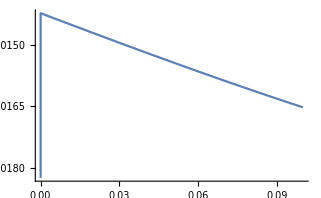

```mathematica
kt={0,1,0};
lt={1+Sqrt[3]/2,0,0};
mt={0,0,1};
nt={0,1,0};

Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT22L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]

Plot[{integrand1[kt,lt,mt+eps{1,1,0},nt]-fullCT22L[kt,lt,mt+eps{1,1,0},nt]},{eps,0,0.1}]
```

#### Threshold 3

-Graphics-

```mathematica
ct3LTD=-(1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3-m[0]))+1/((E0+E1+E2)*(E2+E3-m[0])*(E0+E4-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E5-q[0]))+1/((E0+E1+E2)*(E0+E4-q[0])*(E0+E1+E5-q[0]))+1/((E1+E4+E5)*(E0+E1+E5-q[0])*(E2+E5-q[0]))+1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E3+E4-m[0]-q[0]))+1/((E2+E3-m[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E2+E3-m[0])*(E0+E4+q[0]))+1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E0+E4+q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E2+E5-q[0])*(E0+E4+q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E1+E4+E5) (E2+E3-m[0]))-1/((E0+E1+E2) (E2+E3-m[0]) (E0+E4-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E0+E1+E5-q[0]))-1/((E0+E1+E2) (E0+E4-q[0]) (E0+E1+E5-q[0]))-1/((E1+E4+E5) (E0+E1+E5-q[0]) (E2+E5-q[0]))-1/((E0+E4-q[0]) (E0+E1+E5-q[0]) (E2+E5-q[0]))-1/((E0+E1+E2) (E0+E1+E3-m[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E3-m[0]) (E2+E3-m[0]) (E1+E3+E4-m[0]-q[0]))-1/((E2+E3-m[0]) (E0+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E0+E1+E3-m[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E2+E3-m[0]) (E0+E4+q[0]))-1/((E0+E1+E3-m[0]) (E2+E3-m[0]) (E0+E4+q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E2+E5-q[0]) (E0+E4+q[0])))

```mathematica
ct3integrand1[ks_,ls_,ms_,ns_]:=ct3LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

0

0

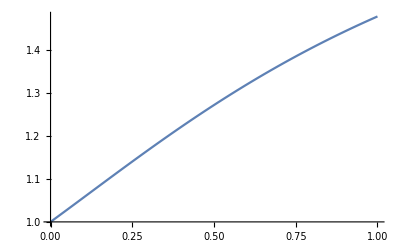

0

```mathematica
rsolct3[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]^2-(myNorm[ns]+myNormMass[ms-ns])^2)/(2*(ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]*(myNorm[ns]+myNormMass[ms-ns])))]

jacquesct3[ks_,ls_,ms_,ns_]:=(Exp[r]*(myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]*(myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])^2-ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ms]))/.{r->rsolct3[ks,ls,ms,ns]}


kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};

N[(myNorm[lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12]
N[(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct3[kt,lt,mt,nt]),12]

Plot[(myNorm[lt]+myNorm[lt-mt-eps{1,1,0}]-myNormMass[mt+eps{1,1,0}-nt]-myNorm[nt])/(jacquesct3[kt,lt,mt+eps{1,1,0},nt]*(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct3[kt,lt,mt+eps{1,1,0},nt])),{eps,0,1}]

N[myNorm[Exp[rsolct3[kt,lt,mt,nt]]*lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]-mt]+myNorm[Exp[rsolct3[kt,lt,mt,nt]]lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-myNormMass[mt-nt]-myNorm[nt],12]
```

```mathematica
fullCT32L[ks_,ls_,ms_,ns_]:=((1/(jacquesct3[ks,ls,ms,ns]*(Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-rsolct3[ks,ls,ms,ns]))*ct3integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->rsolct3[ks,ls,ms,ns]}
```

```mathematica
kt={1,1,0.5};
lt={0,0.5,1};
mt={0.5,3/2,1};
nt={0,1,0};

fullCT32L[kt,lt,mt,nt]
```

0.00463269

-(2 (-90-39 √6+10 √13+3 √78))/((√3 (-1+√2+√3) (1+√2+√3) (-5+4 √2-√13) (-3+2 √2+2 √3-√13) (1+√13) (5+√13) (5+4 √2+√13) (3+2 √2+2 √3+√13)) eps)+O[eps]^0

-(2 (-90-39 √6+10 √13+3 √78))/((√3 (-1+√2+√3) (1+√2+√3) (-5+4 √2-√13) (-3+2 √2+2 √3-√13) (1+√13) (5+√13) (5+4 √2+√13) (3+2 √2+2 √3+√13)) eps)+O[eps]^0

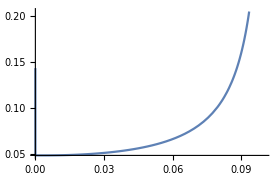

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};
Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT32L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]

Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT32L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

#### Threshold 4

-Graphics-

Two loop

```mathematica
ct4LTD=-(1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3-m[0]))+1/((E1+E4+E5)*(E0+E1+E3-m[0])*(E2+E3-m[0]))+1/((E1+E4+E5)*(E2+E3-m[0])*(E0+E4-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E1+E2+E4-q[0]))+1/((E1+E4+E5)*(E0+E4-q[0])*(E1+E2+E4-q[0]))+1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E2+E5-q[0]))+1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E3+E5-m[0]-q[0]))+1/((E2+E3-m[0])*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E1+E4+E5) (E0+E1+E3-m[0]))-1/((E1+E4+E5) (E0+E1+E3-m[0]) (E2+E3-m[0]))-1/((E1+E4+E5) (E2+E3-m[0]) (E0+E4-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E1+E2+E4-q[0]))-1/((E1+E4+E5) (E0+E4-q[0]) (E1+E2+E4-q[0]))-1/((E0+E1+E2) (E1+E2+E4-q[0]) (E2+E5-q[0]))-1/((E0+E4-q[0]) (E1+E2+E4-q[0]) (E2+E5-q[0]))-1/((E0+E1+E2) (E0+E1+E3-m[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E3-m[0]) (E2+E3-m[0]) (E3+E5-m[0]-q[0]))-1/((E2+E3-m[0]) (E0+E4-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E3+E5-m[0]-q[0])))

```mathematica
ct4integrand1[ks_,ls_,ms_,ns_]:=ct4LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
a4[ks_,ls_,ms_,ns_]:=((myNorm[ks]+myNorm[ks-ls])^2-myNorm[ls]^2)/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2
b4[ks_,ls_,ms_,ns_]:=-2(myNorm[ks]+myNorm[ks-ls])(myNormMass[ms-ns]+myNorm[ns])/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+2*(ls.ms)/Sqrt[myNorm[ks]^2+myNorm[ls]^2]
c4[ks_,ls_,ms_,ns_]:=(myNormMass[ms-ns]+myNorm[ns])^2-myNorm[ms]^2

rsol=Solve[t*myNorm[{kx,ky,kz}]/Sqrt[myNorm[{kx,ky,kz}]^2+myNorm[{lx,ly,lz}]^2]+t*myNorm[{kx,ky,kz}-{lx,ly,lz}]/Sqrt[myNorm[{kx,ky,kz}]^2+myNorm[{lx,ly,lz}]^2]+myNorm[t*{lx,ly,lz}/Sqrt[myNorm[{kx,ky,kz}]^2+myNorm[{lx,ly,lz}]^2]-{mx,my,mz}]-myNormMass[{mx,my,mz}-{nx,ny,nz}]-myNorm[{nx,ny,nz}]==0,t];

rsolct4[ks_,ls_,ms_,ns_]:=Log[(-b4[ks,ls,ms,ns]-Sqrt[b4[ks,ls,ms,ns]^2-4c4[ks,ls,ms,ns] a4[ks,ls,ms,ns]])/(2a4[ks,ls,ms,ns])]
rsolct4Brute[ks_,ls_,ms_,ns_]:=Log[t/.rsol[[1]]]/.{kx->ks[[1]],ky->ks[[2]],kz->ks[[3]],lx->ls[[1]],ly->ls[[2]],lz->ls[[3]],mx->ms[[1]],my->ms[[2]],mz->ms[[3]],nx->ns[[1]],ny->ns[[2]],nz->ns[[3]]}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1+√2+√3-(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2)).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2))+(-(-12+6 √6-(3 √2 (-3+Power[«2»]))/Plus[«3»]-6 √Times[«2»])/(√3)-√(1/3 Power[«2»]-16 Plus[«6»]))/(4 √6)+1/(√(3/(1/32 Plus[«2»]^2+1/64 Plus[«2»]^2)))+√(1+(-1+(Times[«3»]+Times[«2»])/(8 √3))^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[3]/2-Log[(3 (-2/(√3)+(2 (Power[«2»]+Power[«2»]) (Times[«3»]+Power[«2»]))/(√3)-√Plus[«2»]))/(2 (-1+Plus[«2»]^2))].

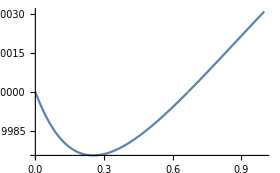

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2))+(-2+((-3+Power[«2»])/(2 Plus[«3»])+√(3+Times[«3»]))^2)/(2 √3 (-1/(√3)+(1/2 Power[«2»] Plus[«2»]+√Plus[«2»])/(√3)))+√(1+(-1+(2+Times[«2»])/(2 √3 Plus[«2»]))^2).

```mathematica
jacquesct4[ks_,ls_,ms_,ns_]:=(Exp[r]*(myNorm[ks]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+myNorm[ks-ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]*(myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])^2-ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ms]))/.{r->rsolct4[ks,ls,ms,ns]}


kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
N[rsolct4[kt,lt,mt,nt],12];
N[rsolct4Brute[kt,lt,mt,nt],12];

N[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12];
N[(myNorm[Exp[rsolct4Brute[kt,lt,mt,nt]]kt]/Sqrt[myNorm[kt]^2+myNorm[lt]^2]+myNorm[Exp[rsolct4Brute[kt,lt,mt,nt]]kt-Exp[rsolct4Brute[kt,lt,mt,nt]]lt]/Sqrt[myNorm[kt]^2+myNorm[lt]^2]+myNorm[Exp[rsolct4Brute[kt,lt,mt,nt]]lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]-mt]-myNormMass[mt-nt]-myNorm[nt]),12];
N[(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct4[kt,lt,mt,nt]),12];

Plot[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt-eps{1,1,0}]-myNormMass[mt+eps{1,1,0}-nt]-myNorm[nt])/(jacquesct4[kt,lt,mt+eps{1,1,0},nt]*(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct4[kt,lt,mt+eps{1,1,0},nt])),{eps,0,1}]

N[myNorm[Exp[rsolct3[kt,lt,mt,nt]]*lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]-mt]+myNorm[Exp[rsolct3[kt,lt,mt,nt]]lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-myNormMass[mt-nt]-myNorm[nt],12];
```

```mathematica
fullCT42L[ks_,ls_,ms_,ns_]:=((1/(jacquesct4[ks,ls,ms,ns]*(Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-rsolct4[ks,ls,ms,ns]))*ct4integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->rsolct4[ks,ls,ms,ns]}
```

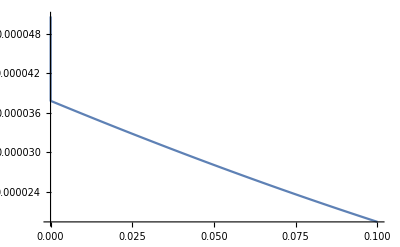

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
(*Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT42L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]*)

Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT42L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

One loop

```mathematica
rsolct5[ks_,ls_,ms_,ns_]:=Log[(myNorm[ls]^2-(myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns])^2)/(2*(myNorm[ks]*(myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns])+ks.ls))*myNorm[ks]]
jacquesct5[ks_,ls_,ms_,ns_]:=(Exp[r]*(1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]ks/myNorm[ks]-ls]))/.{r->rsolct5[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1+√2+√3-(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2)).

0.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[2]/2-Log[(1-Plus[«3»]^2)/(2 (1-1/2 Power[«2»] Plus[«2»]-Power[«2»]))].

0.

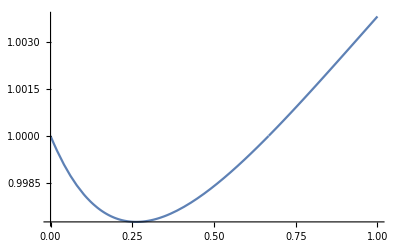

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
N[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12]
N[(Log[myNorm[kt]]-rsolct5[kt,lt,mt,nt]),12]
Plot[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt-eps{1,1,0}]-myNormMass[mt+eps{1,1,0}-nt]-myNorm[nt])/(jacquesct5[kt,lt,mt+eps{1,1,0},nt]*(Log[myNorm[kt]]-rsolct5[kt,lt,mt+eps{1,1,0},nt])),{eps,0,1}]
```

```mathematica
fullCT41L[ks_,ls_,ms_,ns_]:=((1/(jacquesct5[ks,ls,ms,ns]*(Log[myNorm[ks]]-rsolct5[ks,ls,ms,ns]))*ct4integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->rsolct5[ks,ls,ms,ns]}
```

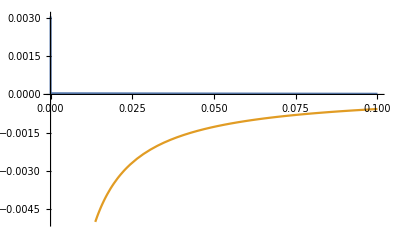

```mathematica
Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT41L[kt,lt,mt+eps{1,0,1},nt],fullCT41L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

#### Threshold 5

-Graphics-

```mathematica
ct5LTD=-(1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3+m[0]))+1/((E1+E4+E5)*(E0+E1+E3+m[0])*(E2+E3+m[0]))+1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E0+E4-q[0]))+1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E0+E4-q[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E2+E5-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))+1/((E1+E4+E5)*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3+m[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E0+E4-q[0]))+1/((E0+E1+E2)*(E2+E3+m[0])*(E2+E5-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E1+E3+E4-m[0]-q[0]))+1/((E1+E4+E5)*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E1+E4+E5) (E0+E1+E3+m[0]))-1/((E0+E1+E2) (E1+E4+E5) (E2+E3+m[0]))-1/((E1+E4+E5) (E0+E1+E3+m[0]) (E2+E3+m[0]))-1/((E0+E1+E2) (E0+E1+E3+m[0]) (E0+E4-q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E0+E4-q[0]))-1/((E0+E1+E3+m[0]) (E2+E3+m[0]) (E0+E4-q[0]))-1/((E0+E1+E2) (E2+E3+m[0]) (E2+E5-q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E2+E5-q[0]))-2/((E2+E3+m[0]) (E0+E4-q[0]) (E2+E5-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5) (E0+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E0+E4-q[0]) (E3+E5-m[0]-q[0]))-1/((E1+E4+E5) (E2+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E3+E5-m[0]-q[0])))

Two loop

```mathematica
ct5integrand1[ks_,ls_,ms_,ns_]:=ct5LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
radius5[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(myNorm[ks]+myNorm[ks-ls]+myNorm[ls])]
jacques5[ks_,ls_,ms_,ns_]:=((myNorm[ks]+myNorm[ks-ls]+myNorm[ls])Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/.{r->radius5[ks,ls,ms,ns]}
```

```mathematica
fullCT52L[ks_,ls_,ms_,ns_]:=((1/(jacques5[ks,ls,ms,ns] (Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*ct5integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->radius5[ks,ls,ms,ns]}
```

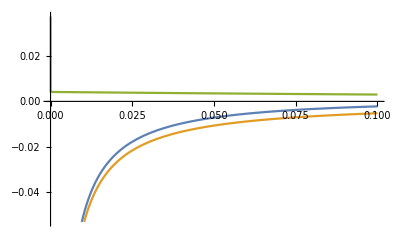

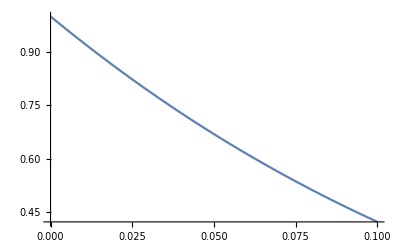

```mathematica
kt={1,0,0};
lt={-1/2,0,1};
mt={0,1,1};
nt={a,a,0}/.{a->(566957-156540 √2-282450 √5+14530 √10-3730 √13+112770 √26+32085 √65-38720 √130-√(1208768726560-438553801896 √2-95049382632 √5+65571421352 √10-52749692552 √13-14120108088 √26+89793904224 √65-70456909480 √130))/977388};


Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt],fullCT52L[kt,lt,mt+eps{1,0,1},nt],integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT52L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]/fullCT52L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

One loop

```mathematica
radius51L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns])^2-myNorm[ls]^2)/(2(-(myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns])-ks.ls/myNorm[ks]))]
jacques51L[ks_,ls_,ms_,ns_]:=(Exp[r]*(1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->radius51L[ks,ls,ms,ns]}
```

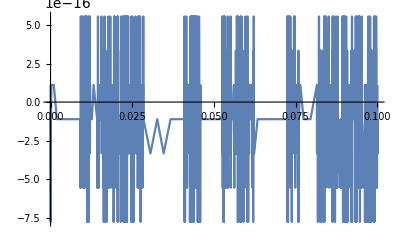

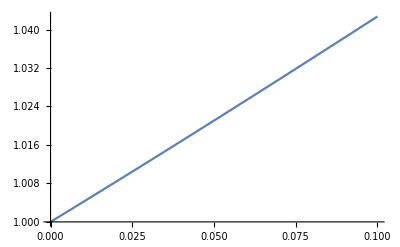

```mathematica
Plot[{((Exp[radius51L[kt,lt,mt+eps{1,0,1},nt]]myNorm[kt]+myNorm[Exp[radius51L[kt,lt,mt+eps{1,0,1},nt]]kt-lt])+myNorm[lt]-myNorm[mt+eps{1,0,1}]-myNormMass[mt+eps{1,0,1}-nt]-myNorm[nt])},{eps,0,0.1}]
Plot[{(jacques51L[kt,lt,mt+eps{1,0,1},nt](Log[myNorm[kt]]-radius51L[kt,lt,mt+eps{1,0,1},nt]))/((myNorm[kt]+myNorm[kt-lt])+myNorm[lt]-myNorm[mt+eps{1,0,1}]-myNormMass[mt+eps{1,0,1}-nt]-myNorm[nt])},{eps,0,0.1}]
```

```mathematica
fullCT51L[ks_,ls_,ms_,ns_]:=((1/(jacques51L[ks,ls,ms,ns] (Log[myNorm[ks]]-r))*ct5integrand1[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->radius51L[ks,ls,ms,ns]}
```

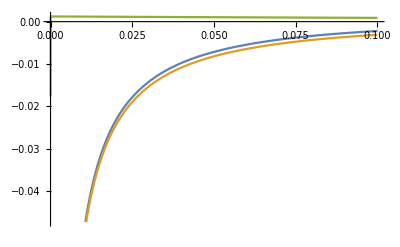

```mathematica
Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt],fullCT51L[kt,lt,mt+eps{1,0,1},nt],integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT51L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

### Full integrand

```mathematica
integrand11L[ks_,ls_,ms_,ns_]:=(fullCT11L[ks,ls,ms,ns]+fullCT41L[ks,ls,ms,ns]+fullCT51L[ks,ls,ms,ns])
integrand12L[ks_,ls_,ms_,ns_]:=(fullCT12L[ks,ls,ms,ns]+fullCT22L[ks,ls,ms,ns]+fullCT32L[ks,ls,ms,ns]+fullCT42L[ks,ls,ms,ns]+fullCT52L[ks,ls,ms,ns])
```

#### MultiChanneling

```mathematica
eSurf1[ks_,ls_,ms_,ns_]:=(myNorm[ls]+myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns])
eSurf2[ks_,ls_,ms_,ns_]:=(2*myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns])
pSurf1[ks_,ls_,ms_,ns_]:=(myNorm[ls]+myNorm[ls-ms]-myNorm[ms])
```

```mathematica
subspaceTheta[ks_,ls_,ms_,ns_]:=HeavisideTheta[eSurf1[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]HeavisideTheta[eSurf2[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]
fullspaceTheta[ks_,ls_,ms_,ns_]:=1-HeavisideTheta[eSurf1[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]HeavisideTheta[eSurf2[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]
```

#### Full Integrand

```mathematica
fullintegrand1[ks_,ls_,ms_,ns_]:=-1/(8 myNorm[ns] myNormMass[ns-ms] myNorm[ms])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ms],ns[[1]],ns[[2]],ns[[3]]}])(integrand1[ks,ls,ms,ns]-subspaceTheta[ks,ls,ms,ns]integrand11L[ks,ls,ms,ns]-fullspaceTheta[ks,ls,ms,ns]integrand12L[ks,ls,ms,ns])
```

## -Graphics-

```mathematica
props2=prop[k,0]*prop[k-l,0]*prop[k+q,0]
diag2=cLTD[props2,loopmom->{k},EvalAll->True];
diag2[[1]]
diag2[[2]]
integrand2[ks_,ls_,ms_,ns_]:=-I*diag2[[1]]/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[k+q,0]

-(ⅈ (-1/((E0+E1+l[0]) (E0+E2-q[0]))-1/((E0+E1-l[0]) (E1+E2-l[0]-q[0]))-1/((E0+E2-q[0]) (E1+E2-l[0]-q[0]))-1/((E0+E1-l[0]) (E0+E2+q[0]))-1/((E0+E1+l[0]) (E1+E2+l[0]+q[0]))-1/((E0+E2+q[0]) (E1+E2+l[0]+q[0]))))/(8 E0 E1 E2)

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(k.k+2 k.q+q.q)}

### Counterterms

#### Threshold 1

-Graphics-

```mathematica
ct6LTD=-(-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0]))/(8 E0 E1 E2)
```

-(-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0]))/(8 E0 E1 E2)

```mathematica
ct1integrand2[ks_,ls_,ms_,ns_]:=ct6LTD/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
fullCT61L[ks_,ls_,ms_,ns_]:=((1/(2*Exp[r](Log[myNorm[ks]]-r))*ct1integrand2[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->Log[(myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns])/2]}
```

0

0

0.138057

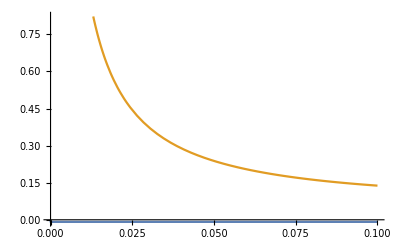

```mathematica
kt={(2+Sqrt[2]+Sqrt[3])/2,0,0};
lt={0,0,1};
mt={0,1,1};
nt={1,1,1};

2*myNorm[kt]-(myNorm[lt]+myNorm[mt-lt]+myNormMass[mt-nt]+myNorm[nt])

(Log[myNorm[kt]]-r)/.{r->Log[(myNorm[lt]+myNorm[mt-lt]+myNormMass[mt-nt]+myNorm[nt])/(2)]}

fullCT61L[kt,lt,mt+0.1{1,0,1},nt]

Plot[{integrand2[kt,lt,mt+eps{1,0,1},nt]-fullCT61L[kt,lt,mt+eps{1,0,1},nt],fullCT61L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

#### Threshold 2

-Graphics-

```mathematica
ct7LTD=-(-1/(E0+E1-l[0])-1/(E0+E2-q[0]))/(8 E0 E1 E2)
```

-(-1/(E0+E1-l[0])-1/(E0+E2-q[0]))/(8 E0 E1 E2)

```mathematica
ct2integrand2[ks_,ls_,ms_,ns_]:=ct7LTD/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
rsol7[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ms]+myNormMass[ms-ns]+myNorm[ns])^2-myNorm[ls]^2)/(2(myNorm[ls-ms]+myNormMass[ms-ns]+myNorm[ns]-ks.ls/myNorm[ks]))]
jacques7[ks_,ls_,ms_,ns_]:=(Exp[r]*(1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->rsol7[ks,ls,ms,ns]}
```

```mathematica
fullCT71L[ks_,ls_,ms_,ns_]:=((1/(jacques7[ks,ls,ms,ns]*(Log[myNorm[ks]]-r))*ct2integrand2[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->rsol7[ks,ls,ms,ns]}
```

-(-1/(1+√2+√3)-1/(-2+2 √3-1/4 √(27-17 √2+√3-√6)-√(3+1/16 (27-17 √2+√3-√6))))/(24 √2)

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+√2+√3-1/4 √(27-17 √2+√3-√6)-√(3+1/16 (27-17 Power[«2»]+√3-Power[«2»])).

0.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[3]/2-Log[(-1+(1+Times[«2»]+Power[«2»])^2)/(2 (1-Power[«2»]+1/4 Power[«2»]+√Plus[«2»]))].

0.

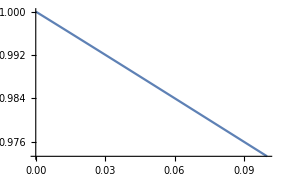

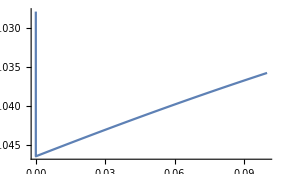

```mathematica
kt={1,1,1};
lt={0,1,0};
mt={0,1,1};
nt={1/4 √(27-17 √2+√3-√6),0,0};

ct2integrand2[kt,lt,mt,nt]
N[myNorm[kt]+myNorm[kt-lt]-myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt],12]
N[Log[myNorm[kt]]-rsol7[kt,lt,mt,nt],12]
Plot[(myNorm[kt]+myNorm[kt-lt]-myNorm[lt-mt-eps{1,0,1}]-myNormMass[mt+eps{1,0,1}-nt]-myNorm[nt])/(jacques7[kt,lt,mt+eps{1,0,1},nt](Log[myNorm[kt]]-rsol7[kt,lt,mt+eps{1,0,1},nt])),{eps,0,0.1}]

Plot[{integrand2[kt,lt,mt+eps{1,1,1/2},nt]-fullCT71L[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

### Full Integrand

```mathematica
integrand21L[ks_,ls_,ms_,ns_]:=(fullCT61L[ks,ls,ms,ns]+fullCT71L[ks,ls,ms,ns])
```

```mathematica
fullintegrand2[ks_,ls_,ms_,ns_]:=1/(16 myNorm[ns] myNormMass[ns-ms] myNorm[ms-ls]myNorm[ls])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls]+myNormMass[ms-ns],ns[[1]],ns[[2]],ns[[3]]}])(integrand2[ks,ls,ms,ns]-integrand21L[ks,ls,ms,ns])
```

## -Graphics-

### Full Integrand

```mathematica
fullintegrand3[ks_,ls_,ms_,ns_]:=1/(32 myNorm[ns] myNormMass[ns-ms] myNorm[ms-ls]myNorm[ls-ks]myNorm[ks])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls]+myNorm[ls-ks],ks[[1]],ks[[2]],ks[[3]]}])1/(MS[{myNorm[ks-ls]+myNorm[ks],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ks-ls]+myNorm[ks],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ks-ls]+myNorm[ks]+myNormMass[ms-ns],ns[[1]],ns[[2]],ns[[3]]}])
```

## Full integrand

```mathematica
fullintegrand[ks_,ls_,ms_,ns_]:=fullintegrand1[ks,ls,ms,ns]+fullintegrand2[ks,ls,ms,ns]+fullintegrand3[ks,ls,ms,ns]
```

## TESTS

### Single threshold

-Graphics-

```mathematica
kt={1+Sqrt[3]/2,0,0};
lt={0,1,0};
mt={0,0,1};
nt={0,1,0};
```

```mathematica
fullintegrand2[kt,lt,mt+0.1{1,0,1},nt]
```

-7.84572×10^-10

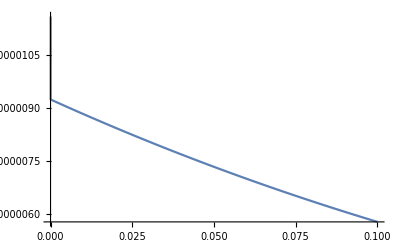

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={0,1,0};
lt={1+Sqrt[3]/2,0,0};
mt={0,0,1};
nt={0,1,0};
```

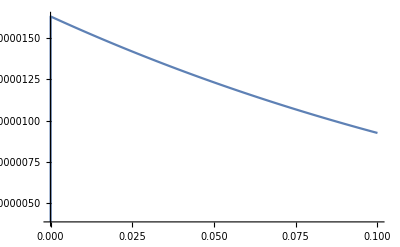

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};
```

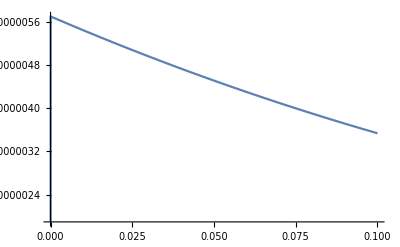

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt](*-fullCT32L[kt,lt,mt+eps{1,0,1},nt],fullCT11L[kt,lt,mt+eps{1,0,1},nt],fullCT12L[kt,lt,mt+eps{1,0,1},nt]*)},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
```

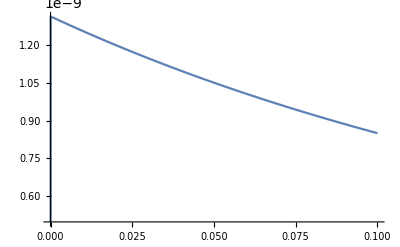

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={1,0,0};
lt={-1/2,0,1};
mt={0,1,1};
nt={a,a,0}/.{a->(566957-156540 √2-282450 √5+14530 √10-3730 √13+112770 √26+32085 √65-38720 √130-√(1208768726560-438553801896 √2-95049382632 √5+65571421352 √10-52749692552 √13-14120108088 √26+89793904224 √65-70456909480 √130))/977388};
```

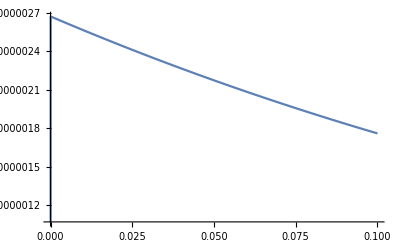

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={(2+Sqrt[2]+Sqrt[3])/2,0,0};
lt={0,0,1};
mt={0,1,1};
nt={1,1,1};
```

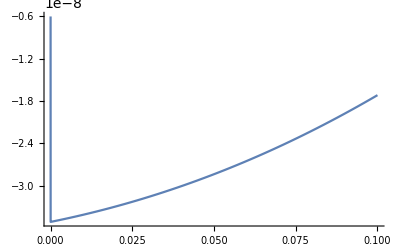

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

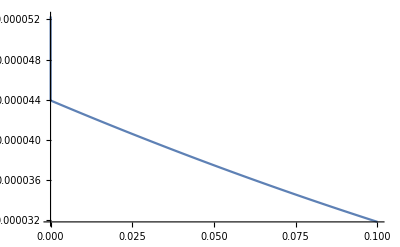

```mathematica
kt={1,1,1};
lt={0,1,0};
mt={0,1,1};
nt={1/4 √(27-17 √2+√3-√6),0,0};


Plot[{fullintegrand[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

### Single Pinches

-Graphics-

```mathematica
kt={0.5,0,0};
lt={1,0,0};
mt={0,0,1};
nt={0,1,0};
```

```mathematica
pSurf1[kt,lt,mt,nt]
```

√2

```mathematica
subspaceTheta[kt,lt,mt,nt]
```

0

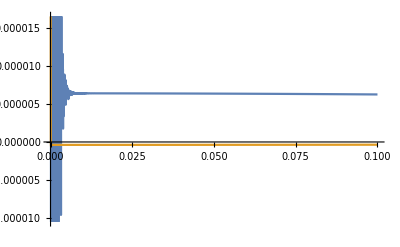

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,0},mt,nt],fullintegrand2[kt,lt+eps{0,1,0},mt,nt]+fullintegrand3[kt,lt+eps{0,1,0},mt,nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
kt={0,0,1};
lt={0.5,0,0};
mt={1,0,0};
nt={0,1,0};
```

```mathematica
subspaceTheta[kt,lt,mt,nt]
```

0

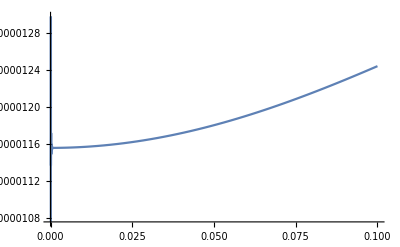

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,0},mt,nt]+fullintegrand2[kt,lt+eps{0,1,0},mt,nt]+fullintegrand3[kt,lt+eps{0,1,0},mt,nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
kt={0.3,0,0};
lt={0.5,0,0};
mt={1,0,0};
nt={0,1,0};
```

```mathematica
pSurf1[kt,lt,mt,nt]
```

0.

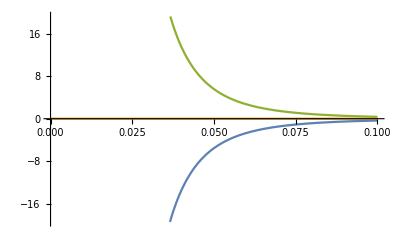

```mathematica
Plot[{fullCT11L[kt,lt+eps{0,1,1},mt,nt],fullCT41L[kt,lt+eps{0,1,1},mt,nt],fullCT51L[kt,lt+eps{0,1,1},mt,nt]},{eps,0,0.1}]
```

```mathematica
(*fullintegrand1[ks_,ls_,ms_,ns_]:=-1/(8 myNorm[ns] myNormMass[ns-ms] myNorm[ms])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ms],ns[[1]],ns[[2]],ns[[3]]}])(0*integrand1[ks,ls,ms,ns]-subspaceTheta[ks,ls,ms,ns]integrand11L[ks,ls,ms,ns]-fullspaceTheta[ks,ls,ms,ns]integrand12L[ks,ls,ms,ns])
fullintegrand2[ks_,ls_,ms_,ns_]:=1/(16 myNorm[ns] myNormMass[ns-ms] myNorm[ms-ls]myNorm[ls])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls]+myNormMass[ms-ns],ns[[1]],ns[[2]],ns[[3]]}])(0*integrand2[ks,ls,ms,ns]-integrand21L[ks,ls,ms,ns])*)
```

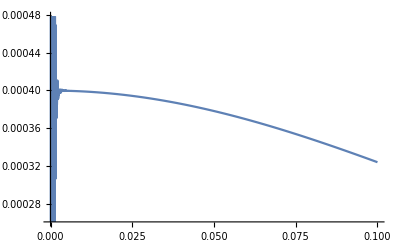

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,0},mt,nt]+fullintegrand3[kt,lt+eps{0,1,0},mt,nt]+fullintegrand2[kt,lt+eps{0,1,0},mt,nt],},{eps,0,0.1}]
```